# Old 3D Footed Simulation Model with Reduction using MEX

## Initialization

```mathematica
dl1=DateString[]
```

Tue 23 Jul 2013 15:50:22

```mathematica
nbdir=NotebookDirectory[]
```

/home/rsinnet/Documents/MATLAB/kneefoot3d-sva-v30/

```mathematica
snakeyamldir=FileNameJoin[{nbdir,"third","snakeyaml"}];
utildir=FileNameJoin[{nbdir,"util"}];
screwsdir=FileNameJoin[{nbdir,"third","Screws"}];
```

```mathematica
$Path = DeleteDuplicates[Join[$Path,{utildir,snakeyamldir,screwsdir}]]
```

{/usr/local/Wolfram/Mathematica/8.0/SystemFiles/Links,/home/rsinnet/.Mathematica/Kernel,/home/rsinnet/.Mathematica/Autoload,/home/rsinnet/.Mathematica/Applications,/usr/share/Mathematica/Kernel,/usr/share/Mathematica/Autoload,/usr/share/Mathematica/Applications,.,/home/rsinnet,/usr/local/Wolfram/Mathematica/8.0/AddOns/Packages,/usr/local/Wolfram/Mathematica/8.0/AddOns/LegacyPackages,/usr/local/Wolfram/Mathematica/8.0/SystemFiles/Autoload,/usr/local/Wolfram/Mathematica/8.0/AddOns/Autoload,/usr/local/Wolfram/Mathematica/8.0/AddOns/Applications,/usr/local/Wolfram/Mathematica/8.0/AddOns/ExtraPackages,/usr/local/Wolfram/Mathematica/8.0/SystemFiles/Kernel/Packages,/usr/local/Wolfram/Mathematica/8.0/Documentation/English/System,/home/rsinnet/Documents/MATLAB/kneefoot3d-sva-v30/util,/home/rsinnet/Documents/MATLAB/kneefoot3d-sva-v30/third/snakeyaml,/home/rsinnet/Documents/MATLAB/kneefoot3d-sva-v30/third/Screws}

```mathematica
Needs["RobotLinks`"]
```

```mathematica
Needs["SnakeYaml`"]
SnakeYaml`YamlInit[FileNameJoin[{snakeyamldir,"snakeyaml-1.10.jar"}]]
```

Yaml already initizialized

```mathematica
builddir=FileNameJoin[{nbdir,"build_"<>FileBaseName[NotebookFileName[]]}]
```

/home/rsinnet/Documents/MATLAB/kneefoot3d-sva-v30/build_old-model-3d-feet-amber-suite

```mathematica
If[DirectoryQ[builddir],,CreateDirectory[builddir]];
```

```mathematica
constsubs={
Lft->1/4, (* foot ankle–toe length *)
Lfh->(1 1)/(4 4), (* foot ankle–heel length *)
ha->(1 1)/(5 2),(* height of ankle *)
Lc->0.50,(* calf length *)
Lt->0.50,(* thigh length *)
rfx->-(2 1)/(3 6),(* foot CoM x *)
rfz->(2 1 1)/(3 3 6),(* foot CoM z *)
rcx->0,(* calf CoM x *)
rcz->0.375,(* calf CoM z *)
rtx->0,(* thigh CoM x *)
rtz->0.175,(* thigh CoM z *)
rTx->0, (* torso CoM x *)
rTz->0.075,(* torso CoM z *)
wHip->0.25 p[1],
wFoot->0.08p[1],
mf->0.1,
mc->1.5,
mt->5,
mT->20,
g->9.81,
α->p[2]
}//Rationalize
```

{Lft→1/4,Lfh→1/16,ha→1/10,Lc→1/2,Lt→1/2,rfx→-1/9,rfz→1/27,rcx→0,rcz→3/8,rtx→0,rtz→7/40,rTx→0,rTz→3/40,wHip→(p(1))/4,wFoot→(2 p(1))/25,mf→1/10,mc→3/2,mt→5,mT→20,g→981/100,α→p(2)}

```mathematica
np=3;(* Number of parameters that can be passed in p arugment. *)
```

#### State space

```mathematica
Qb={Subscript[p, x][t],Subscript[p, y][t],Subscript[p, z][t],Subscript[q, z][t],Subscript[q, x][t],Subscript[q, y][t]};
dQb=D[Qb, t];
Xb=Join[Qb,dQb];
nb=Length[Qb];
```

```mathematica
nr=8;
Qr=(Subscript[q, #1][t]&)/@Range[nr]
dQr=D[Qr, t];
Xr=Join[Qr,dQr];
```

{q_1(t),q_2(t),q_3(t),q_4(t),q_5(t),q_6(t),q_7(t),q_8(t)}

```mathematica
nl=nr+1; (* Number of rigid links. *)
nc=1; (* Number of cyclic variables. *)
ns=nr-nc; (* Number of shape variables. *)
```

```mathematica
Q=Join[Qb,Qr];
dQ=Join[dQb,dQr];
X=Join[Q,dQ];
ne=Length[Q];
```

#### Subs for absolute coordinates

MATLAB shall pass the absolute coordinates as though they were relative coordinates according to this substitution list. It is a trivial pattern replacement.

```mathematica
ζxsubs=((Qr⟦#⟧/.q->ζ)->Qr⟦#⟧&)/@Range[2,7];
dζxsubs=D[ζxsubs,t];
Ζxsubs=Join[ζxsubs,dζxsubs];
```

```mathematica
statesubs=Join[(Q⟦#⟧->q[#]&/@Range[ne]),(dQ⟦#⟧->dq[#]&/@Range[ne])]
```

{p_x(t)→q(1),p_y(t)→q(2),p_z(t)→q(3),q_z(t)→q(4),q_x(t)→q(5),q_y(t)→q(6),q_1(t)→q(7),q_2(t)→q(8),q_3(t)→q(9),q_4(t)→q(10),q_5(t)→q(11),q_6(t)→q(12),q_7(t)→q(13),q_8(t)→q(14),p_x'(t)→dq(1),p_y'(t)→dq(2),p_z'(t)→dq(3),q_z'(t)→dq(4),q_x'(t)→dq(5),q_y'(t)→dq(6),q_1'(t)→dq(7),q_2'(t)→dq(8),q_3'(t)→dq(9),q_4'(t)→dq(10),q_5'(t)→dq(11),q_6'(t)→dq(12),q_7'(t)→dq(13),q_8'(t)→dq(14)}

```mathematica
mm={mf,0,mc,mt,mT,mt,mc,0,mf}/.constsubs;
```

#### Useful functions

```mathematica
CrossProd[Ω_]:={Ω⟦3,2⟧,Ω⟦1,3⟧,Ω⟦2,1⟧};
```

```mathematica
ParallelSimplify[A_?MatrixQ]:=ParallelTable[Simplify[A⟦i,j⟧],{i,Dimensions[A]⟦1⟧},{j,Dimensions[A]⟦2⟧}]
ParallelSimplify[A_?VectorQ]:=ParallelTable[Simplify[A⟦i⟧],{i,Length[A]}]
ParallelSimplify[A_]:=Simplify[A]
```

```mathematica
ParallelFullSimplify[A_?MatrixQ]:=ParallelTable[FullSimplify[A⟦i,j⟧],{i,Dimensions[A]⟦1⟧},{j,Dimensions[A]⟦2⟧}]
ParallelFullSimplify[A_?VectorQ]:=ParallelTable[FullSimplify[A⟦i⟧],{i,Length[A]}]
ParallelFullSimplify[A_]:=FullSimplify[A]
```

```mathematica
AxisScalarToVector[axis_]:=Sign[axis]UnitVector[3,Abs[axis]]
```

```mathematica
BlockDiagonalMatrix:=(SparseArray[Band[{1,1}]->{##}]//Normal)&
```

#### Write files to disk

```mathematica
WriteExpr[expr_,fname_?StringQ]:={
stream=OpenWrite[FileNameJoin[{builddir,fname<>".math"}]];
Write[stream,expr/.statesubs];
Close[stream];
Clear[stream];
}
```

```mathematica
WriteExprζ[expr_,fname_?StringQ]:=WriteExpr[expr/.Ζxsubs,fname]
```

wHip=-1 is left left stance

### Compatibility with amber_suite

#### Hash maps

```mathematica
AxisToVector["x"]={1,0,0};
AxisToVector["y"]={0,1,0};
AxisToVector["z"]={0,0,1};
```

#### Prismatic Twists

```mathematica
GetTwist[origin_?VectorQ/;Length[origin]==3,axis_?StringQ/;StringMatchQ[axis,RegularExpression["-?P[x-z]"]]]:=PrismaticTwist[origin,
If[StringMatchQ[StringTake[axis,1],"-"],-1,+1]*AxisToVector[StringTake[axis,-1]]]
```

#### RevoluteTwists

```mathematica
GetTwist[origin_?VectorQ/;Length[origin]==3,axis_?StringQ/;StringMatchQ[axis,RegularExpression["-?R[x-z]"]]]:=RevoluteTwist[origin,If[StringMatchQ[StringTake[axis,1],"-"],-1,+1]*AxisToVector[StringTake[axis,-1]]]
```

## Physical Configuration

The configuration in this section is emitted as YAML for the SVA model. The configuration is also important for later sections in this file.

```mathematica
TwistAxesBase={"Px","Py","Pz","Rz","Rx","Ry"};
TwistAxesRobot=Flatten@@(Join[#1,Reverse[(StringTake[#1,-2]&)/@#1]]&)/@{{"-Rx","-Ry","-Ry","-Ry"}};
TwistAxesExt=Join[TwistAxesBase,TwistAxesRobot]
```

{Px,Py,Pz,Rz,Rx,Ry,-Rx,-Ry,-Ry,-Ry,Ry,Ry,Ry,Rx}

```mathematica
JointOffsetsSTT={
{-Lft,0,ha},
{0,0,0},
{0,0,Lc},
{0,0,Lt},
{0,wHip,0},
{0,0,-Lt},
{0,0,-Lc},
{0,0,0},
{Lft,0,-ha}
}/.constsubs;
```

Compute the origins of the joints relative to the stance toe

```mathematica
JointOriginsSTT=Accumulate[JointOffsetsSTT];
```

```mathematica
ComOffsetsSTT={
{rfx,0,rfz},
{0,0,0},
{rcx,0,rcz},
{rtx,0,rtz},
{rTx,wHip/2,rTz},
{rtx,0,-Lt+rtz},
{rcx,0,-Lc+rcz},
{0,0,0},
{Lft+rfx,0,-ha+rfz}
}/.constsubs;
```

```mathematica
ComOriginsSTT=Join[
ComOffsetsSTT⟦{1}⟧,
Table[(JointOriginsSTT⟦i-1⟧+ComOffsetsSTT⟦i⟧),{i,2,nr+1}]
]
```

(-1/9 | 0 | 1/27
-1/4 | 0 | 1/10
-1/4 | 0 | 19/40
-1/4 | 0 | 31/40
-1/4 | (p(1))/8 | 47/40
-1/4 | (p(1))/4 | 31/40
-1/4 | (p(1))/4 | 19/40
-1/4 | (p(1))/4 | 1/10
-1/9 | (p(1))/4 | 1/27)

## Dynamics

### Kinematics

#### Empty twist

```mathematica
ξ0={0,0,0,0,0,0};
```

#### Base frame twists

```mathematica
ξbf=(GetTwist[{0,0,0},#1]&)/@TwistAxesBase
```

(1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0)

#### Robot twists from stance foot

```mathematica
ξrf=GetTwist[JointOriginsSTT⟦#1⟧,TwistAxesRobot⟦#1⟧]&/@(Range[nr])
```

(0 | -1/10 | 0 | -1 | 0 | 0
1/10 | 0 | 1/4 | 0 | -1 | 0
3/5 | 0 | 1/4 | 0 | -1 | 0
11/10 | 0 | 1/4 | 0 | -1 | 0
-11/10 | 0 | -1/4 | 0 | 1 | 0
-3/5 | 0 | -1/4 | 0 | 1 | 0
-1/10 | 0 | -1/4 | 0 | 1 | 0
0 | 1/10 | -(p(1))/4 | 1 | 0 | 0)

#### Base configuration

```mathematica
gf[0]=RPToHomogeneous[IdentityMatrix[3],#1]&/@ComOriginsSTT;
```

```mathematica
GetStanceTwists[massIndex_?IntegerQ/;0<massIndex≤nl]:=Join[
{{ξbf⟦nb⟧,Q⟦nb⟧}},
({ξrf⟦#⟧,Qr⟦#⟧}&)/@Range[massIndex-1]
];
```

```mathematica
FK:=Function[{twists, g},ForwardKinematics@@Join[twists,{g}]]
```

#### Calculate the forward kinematics

```mathematica
gf[θ]=(FK[GetStanceTwists[#1],gf[0]⟦#1⟧]&)/@Range[nl];
```

### Dynamics

#### Convert to absolute coordinates, WAY FASTER

```mathematica
nζ=nr-2;
```

```mathematica
Τ=SparseArray[{{i_,j_}/;((j≤nζ/2)&&(i≥j))->1,{i_,j_}/;((j>nζ/2)&&(i≥j))->-1},{nζ,nζ}];
```

```mathematica
ζsubs=Solve[((Qr⟦2;;7⟧/.q->ζ)⟦#⟧==(Τ.Qr⟦2;;7⟧)⟦#⟧&)/@Range[nζ],Qr⟦2;;7⟧]//Flatten;
dζsubs=D[ζsubs,t];
Ζsubs=Join[ζsubs,dζsubs];
```

```mathematica
Ζr=Join[{Subscript[q, 1][t]},(Qr⟦2;;7⟧/.q->ζ),{Subscript[q, 8][t]}];
dΖr=D[Ζr,t];
```

#### Calculate the kinetic energy and manipulator inertia matrix

```mathematica
vf=(ParallelSimplify[D[RigidPosition[#1], {t}]]&)/@gf[θ];
```

```mathematica
vfζ=vf/.Ζsubs//ParallelSimplify;
```

```mathematica
Tfζ=1/2 Tr[vfζᵀ.DiagonalMatrix[mm].vfζ];
```

```mathematica
Dfζ=D[Tfζ,{dΖr,2}]//ParallelSimplify;
WriteExprζ[Dfζ,"Mrzmat"];
```

```mathematica
DfζAug=BlockDiagonalMatrix[{{0}},ParallelSimplify[(Dfζ⟦2;;nr,{1}⟧.Dfζ⟦{1},2;;nr⟧)/Dfζ⟦1,1⟧]];
```

```mathematica
Dαζ=Dfζ+DfζAug;
(*WriteExprζ[Dαζ,"Mazmat"];*)
```

#### Calculate Coriolis matrix

```mathematica
Cfζ=InertiaToCoriolis[Dfζ,Ζr,dΖr]//ParallelSimplify;
WriteExprζ[Cfζ,"Crzmat"];
```

```mathematica
Cαζ=InertiaToCoriolis[Dαζ,Ζr,dΖr];
WriteExprζ[Cαζ,"Cazmat"];
```

#### Calculate the potential energy and 𝒢 matrix

```mathematica
sagittalRestriction={Subscript[q, x][t]->0,Subscript[q, z][t]->0,Subscript[q, 1][t]->0,Subscript[q, 8][t]->0};
```

```mathematica
Vf=Simplify[(g/.constsubs) mm.gf[θ]⟦;;,3,4⟧];
Vfζ=Vf/.Ζsubs//Simplify;
```

```mathematica
G2Dζ=ParallelSimplify[D[Vf/.sagittalRestriction,{{Qr}ᵀ}]/.Ζsubs];
WriteExprζ[G2Dζ,"G2Dzmat"];
```

```mathematica
Vfctζ=Vfζ/.sagittalRestriction
```

1/120000 109 (sin(q_y(t)) (176715 sin(ζ_2(t))+153090 sin(ζ_3(t))+16200 sin(ζ_4(t))-26190 sin(ζ_5(t))-2565 sin(ζ_6(t))-68 sin(ζ_7(t))-150 cos(ζ_7(t))+89490)+cos(q_y(t)) (150 sin(ζ_7(t))+176715 cos(ζ_2(t))+153090 cos(ζ_3(t))+16200 cos(ζ_4(t))-26190 cos(ζ_5(t))-2565 cos(ζ_6(t))-68 cos(ζ_7(t))+35788))

```mathematica
λ=-α Subscript[q, 1][t]/.constsubs;
```

```mathematica
Gfζ=ParallelSimplify[D[Vfζ,{{Ζr}ᵀ}]];
WriteExprζ[Gfζ,"Grzmat"];
```

```mathematica
Gαζ=ParallelSimplify[D[(Vfctζ-1/2 λ^2/Dfζ⟦1,1⟧), {{Ζr}ᵀ}]];
(*WriteExprζ[Gαζ,"Gazmat"];*)
```

```mathematica
Wαζ=λ/Dfζ⟦1,1⟧Dfζ⟦1,2;;nr⟧.dΖr⟦2;;All⟧;
```

```mathematica
ELWαζ=D[D[-Wαζ,{{dΖr}ᵀ}],t]-D[-Wαζ,{{Ζr}ᵀ}];
(*WriteExprζ[ELWαζ,"ELWazmat"];*)
```

#### Check transformation

```mathematica
Τf=BlockDiagonalMatrix[{{1}},Τ,{{1}}]
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 1 | 1 | 0 | 0 | 0 | 0
0 | 1 | 1 | 1 | -1 | 0 | 0 | 0
0 | 1 | 1 | 1 | -1 | -1 | 0 | 0
0 | 1 | 1 | 1 | -1 | -1 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
Τf.Qr
```

{q_1(t),q_2(t),q_2(t)+q_3(t),q_2(t)+q_3(t)+q_4(t),q_2(t)+q_3(t)+q_4(t)-q_5(t),q_2(t)+q_3(t)+q_4(t)-q_5(t)-q_6(t),q_2(t)+q_3(t)+q_4(t)-q_5(t)-q_6(t)-q_7(t),q_8(t)}

```mathematica
ζζsubs=((Qr⟦2;;7⟧/.q->ζ)⟦#⟧->(Τ.Qr⟦2;;7⟧)⟦#⟧&)/@Range[nζ]
```

{ζ_2(t)→q_2(t),ζ_3(t)→q_2(t)+q_3(t),ζ_4(t)→q_2(t)+q_3(t)+q_4(t),ζ_5(t)→q_2(t)+q_3(t)+q_4(t)-q_5(t),ζ_6(t)→q_2(t)+q_3(t)+q_4(t)-q_5(t)-q_6(t),ζ_7(t)→q_2(t)+q_3(t)+q_4(t)-q_5(t)-q_6(t)-q_7(t)}

```mathematica
SeedRandom[1];
testq=Join[X⟦#⟧->Random[]&/@Range[Length[X]],{p[1]->-1,p[2]->15,p[3]->25}]
```

{p_x(t)→0.668693,p_y(t)→0.8312,p_z(t)→0.781807,q_z(t)→0.124634,q_x(t)→0.934537,q_y(t)→0.600252,q_1(t)→0.758355,q_2(t)→0.969089,q_3(t)→0.125699,q_4(t)→0.575636,q_5(t)→0.755052,q_6(t)→0.821438,q_7(t)→0.604601,q_8(t)→0.194465,p_x'(t)→0.657307,p_y'(t)→0.559559,p_z'(t)→0.836731,q_z'(t)→0.160536,q_x'(t)→0.854436,q_y'(t)→0.945436,q_1'(t)→0.937182,q_2'(t)→0.260917,q_3'(t)→0.727288,q_4'(t)→0.279132,q_5'(t)→0.268489,q_6'(t)→0.429717,q_7'(t)→0.94548,q_8'(t)→0.154498,p(1)→-1,p(2)→15,p(3)→25}

```mathematica
testζ=Join[Join[ζζsubs,D[ζζsubs,t]]/.testq,testq⟦{6,7,14,20,21,28,29,30,31}⟧]
```

{ζ_2(t)→0.969089,ζ_3(t)→1.09479,ζ_4(t)→1.67042,ζ_5(t)→0.915372,ζ_6(t)→0.0939335,ζ_7(t)→-0.510667,ζ_2'(t)→0.260917,ζ_3'(t)→0.988205,ζ_4'(t)→1.26734,ζ_5'(t)→0.998847,ζ_6'(t)→0.56913,ζ_7'(t)→-0.37635,q_y(t)→0.600252,q_1(t)→0.758355,q_8(t)→0.194465,q_y'(t)→0.945436,q_1'(t)→0.937182,q_8'(t)→0.154498,p(1)→-1,p(2)→15,p(3)→25}

```mathematica
Tf=1/2 Tr[vfᵀ.DiagonalMatrix[mm].vf];
```

```mathematica
Df=D[Tf,{dQr,2}];
```

```mathematica
Cf=InertiaToCoriolis[Df,Qr,dQr];
```

```mathematica
Round[(Df/.testq)-(Τfᵀ.Dfζ.Τf/.testζ//N),1*^-14]
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
Round[(Cf/.testq)-(Τfᵀ.Cfζ.Τf/.testζ//N),1*^-13]
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
Gf=D[Vf,{{Qr}ᵀ}];
```

```mathematica
Round[(Gf/.testq)-(Τfᵀ.Gfζ/.testζ//N),1*^-13]
```

(0
0
0
0
0
0
0
0)

```mathematica
Wα=λ/Df⟦1,1⟧Df⟦1,2;;nr⟧.dQr⟦2;;All⟧;
ELWα=D[D[-Wα,{{dQr}ᵀ}],t]-D[-Wα,{{Qr}ᵀ}];
```

```mathematica
Round[(ELWα/.testq)-(Τfᵀ.ELWαζ/.testζ//N),1*^-13]
```

(0
0
0
0
0
0
0
0)

```mathematica
Τf.Qr
```

{q_1(t),q_2(t),q_2(t)+q_3(t),q_2(t)+q_3(t)+q_4(t),q_2(t)+q_3(t)+q_4(t)-q_5(t),q_2(t)+q_3(t)+q_4(t)-q_5(t)-q_6(t),q_2(t)+q_3(t)+q_4(t)-q_5(t)-q_6(t)-q_7(t),q_8(t)}

### Reduction surface stabilizer

```mathematica
DDfχ=D[Df⟦1,;;⟧, {Qr⟦2;;nr⟧}]//ParallelSimplify;
```

```mathematica
yz=Subscript[q, 1]'[t]+(-λ+Df⟦1,2;;nr⟧.dQr⟦2;;nr⟧)/Df⟦1,1⟧;
```

```mathematica
yz/.testq
```

2.2607

```mathematica
D[yz,Subscript[q, 1][t]]/.testq
```

2.12278

```mathematica
Dyϕ=α/Df⟦1,1⟧/.constsubs/.testq
```

2.12278

```mathematica
D[yz, {Qr⟦2;;nr⟧}]/.testq
```

{4.19621,2.10849,0.180002,0.105522,-0.00616218,-0.00126582,0.000884159}

```mathematica
Dyχ=-(D[Df⟦1,1⟧, {Qr⟦2;;nr⟧}] (-λ+Df⟦1,2;;nr⟧.dQr⟦2;;nr⟧))/Df⟦1,1⟧^2+(Transpose[D[Df⟦1,2;;nr⟧, {Qr⟦2;;nr⟧}]].dQr⟦2;;nr⟧)/Df⟦1,1⟧/.constsubs/.testq
```

{4.19621,2.10849,0.180002,0.105522,-0.00616218,-0.00126582,0.000884159}

```mathematica
Dydϕ=1/.testq
```

1

```mathematica
D[yz, {dQr⟦1⟧}]/.testq
```

1

```mathematica
Dydχ=1/Df⟦1,1⟧Df⟦1,2;;nr⟧/.testq
```

{-0.460305,-0.218298,0.0426328,-0.0690361,-0.00108626,-0.000306204,-0.000324621}

```mathematica
D[yz, {dQr⟦2;;nr⟧}]/.testq
```

{-0.460305,-0.218298,0.0426328,-0.0690361,-0.00108626,-0.000306204,-0.000324621}

```mathematica
(*WriteExpr[DDfχ,"DM1Dqmat"];*)
```

## Forward and inverse kinematics

This section contains some calculations for calculating forward kinematics of a few specific end-effectors as well as inverse kinematics calculations for use with the reset map and fsolve.

#### End-effector configurations

```mathematica
EffOriginsFoot={
{0,-wFoot/2,0},
{0,wFoot/2,0},
{-Lft-Lfh,-wFoot/2,0},
{-Lft-Lfh,wFoot/2,0},
{0,0,0},
{-Lft-Lfh,0,0},
{-Lft,0,ha},
{-Lft,0,ha+Lc},
{-Lft,0,ha+Lc+Lt},
{-Lft,wHip/2,ha+Lc+Lt},
{-Lft,wHip/2,ha+Lc+Lt+rTz},
{-Lft,wHip,ha+Lc+Lt},
{-Lft,wHip,ha+Lc},
{-Lft,wHip,ha},
{-Lft-Lfh,wHip,0},
{0,wHip,0},
{-Lft-Lfh,wHip+wFoot/2,0},
{-Lft-Lfh,wHip-wFoot/2,0},
{0,wHip+wFoot/2,0},
{0,wHip-wFoot/2,0}
}/.constsubs;
```

```mathematica
nEff=Length[EffOriginsFoot];
```

```mathematica
(EffList={
{"stto","stti","stho","sthi","stt","sth","sta","stk","stH","Tb","Tt","nsH","nsk","nsa","nsh","nst","nshi","nsho","nsti","nsto"},
{1,1,1,1,1,1,1,3,4,5,5,6,7,9,9,9,9,9,9,9}
}//Transpose)ᵀ
```

(stto | stti | stho | sthi | stt | sth | sta | stk | stH | Tb | Tt | nsH | nsk | nsa | nsh | nst | nshi | nsho | nsti | nsto
1 | 1 | 1 | 1 | 1 | 1 | 1 | 3 | 4 | 5 | 5 | 6 | 7 | 9 | 9 | 9 | 9 | 9 | 9 | 9)

```mathematica
EffLabelMap[JLabel_]:=Position[EffList⟦;;,1⟧,JLabel,1]⟦1,1⟧
```

```mathematica
geff[0]=RPToHomogeneous[IdentityMatrix[3],#1]&/@EffOriginsFoot;
```

```mathematica
baseTwistArguments={ξbf⟦#1⟧,Qb⟦#1⟧}&/@Range[nb-1];
```

```mathematica
GetExtStanceTwists[bodyNumber_?IntegerQ/;0<bodyNumber≤nr+1]:=(Join[baseTwistArguments,GetStanceTwists[bodyNumber]])
```

```mathematica
geff[θ]=(FK[GetExtStanceTwists[EffList⟦#1,2⟧],geff[0]⟦#1⟧]&)/@Range[nEff];
```

```mathematica
peff=ParallelFullSimplify[RigidPosition[#1]&]/@geff[θ];
```

```mathematica
veff=D[peff,t];
```

```mathematica
Reff=RigidOrientation[#1]&/@geff[θ];
```

```mathematica
ωeff=(CrossProd[D[#1, t].#1ᵀ]&)/@Reff;
```

```mathematica
Rstt=Reff⟦EffLabelMap["stt"]⟧
```

(cos(q_y(t)) cos(q_z(t))-sin(q_x(t)) sin(q_y(t)) sin(q_z(t)) | -cos(q_x(t)) sin(q_z(t)) | cos(q_z(t)) sin(q_y(t))+cos(q_y(t)) sin(q_x(t)) sin(q_z(t))
cos(q_z(t)) sin(q_x(t)) sin(q_y(t))+cos(q_y(t)) sin(q_z(t)) | cos(q_x(t)) cos(q_z(t)) | sin(q_y(t)) sin(q_z(t))-cos(q_y(t)) cos(q_z(t)) sin(q_x(t))
-cos(q_x(t)) sin(q_y(t)) | sin(q_x(t)) | cos(q_x(t)) cos(q_y(t)))

```mathematica
Subscript[q, y][t]->ArcTan[Rstt⟦3,3⟧,-Rstt⟦3,1⟧]
Subscript[q, z][t]->ArcTan[Rstt⟦2,2⟧,-Rstt⟦1,2⟧]
Subscript[q, x][t]->ArcTan[Rstt⟦3,3⟧,Cos[Subscript[q, y][t]]Rstt⟦3,2⟧]
```

q_y(t)→tan^-1(cos(q_x(t)) cos(q_y(t)),cos(q_x(t)) sin(q_y(t)))

q_z(t)→tan^-1(cos(q_x(t)) cos(q_z(t)),cos(q_x(t)) sin(q_z(t)))

q_x(t)→tan^-1(cos(q_x(t)) cos(q_y(t)),sin(q_x(t)) cos(q_y(t)))

```mathematica
Solve[(ωeff⟦EffLabelMap["stt"]⟧//FullSimplify)=={wx,wy,wz},dQ⟦4;;6⟧]ᵀ//FullSimplify//MatrixForm
```

(q_z'(t)→tan(q_x(t)) (wx sin(q_z(t))-wy cos(q_z(t)))+wz
q_x'(t)→wx cos(q_z(t))+wy sin(q_z(t))
q_y'(t)→sec(q_x(t)) (wy cos(q_z(t))-wx sin(q_z(t))))

```mathematica
pstt=peff⟦EffLabelMap["stt"]⟧;
pnsh=peff⟦EffLabelMap["nsh"]⟧;
```

```mathematica
WriteExpr[pstt,"pstt"];
WriteExpr[pnsh,"pnsh"];
```

```mathematica
pnst=peff⟦EffLabelMap["nst"]⟧;
vnst=veff⟦EffLabelMap["nst"]⟧;
Rnst=Reff⟦EffLabelMap["nst"]⟧;
ωnst=ωeff⟦EffLabelMap["nst"]⟧;
```

```mathematica
WriteExpr[pnst,"pnst"];
WriteExpr[vnst,"vnst"];
WriteExpr[Rnst,"Rnst"];
WriteExpr[ωnst,"wnst"];
```

### x-position of the hip for the stance heel lift controller with the sagittal restriction applied

```mathematica
peffζ=peff/.Ζsubs//ParallelSimplify;
```

```mathematica
pHipX=FullSimplify[peff⟦EffLabelMap["Tb"]⟧⟦1⟧-peff⟦EffLabelMap["sta"]⟧⟦1⟧/.sagittalRestriction]
```

-cos((q_3(t))/2) sin(-q_y(t)+q_2(t)+(q_3(t))/2)

```mathematica
WriteExpr[pHipX,"pHipX"];
```

### Plot positions

```mathematica
pp=Transpose[(peff⟦EffLabelMap[#1]⟧&)/@{
"stti","stto","sta","stto","stho","sta","stho","sthi","sta","sthi","stti","sta",
"stk","stH","Tb","Tt","Tb","nsH","nsk",
"nsa","nsti","nshi","nsa","nshi","nsho","nsa","nsho","nsto","nsa","nsto","nsti"}];
(*WriteExpr[pp,"plotpos"];*)
```

```mathematica
ppζ=Transpose[(peffζ⟦EffLabelMap[#1]⟧&)/@{
"stti","stto","sta","stto","stho","sta","stho","sthi","sta","sthi","stti","sta",
"stk","stH","Tb","Tt","Tb","nsH","nsk",
"nsa","nsti","nshi","nsa","nshi","nsho","nsa","nsho","nsto","nsa","nsto","nsti"}];
WriteExprζ[ppζ,"plotposz"];
```

```mathematica
npp=Dimensions[ppζ]⟦2⟧
```

31

### Flat heel controller

#### Expressions for keeping the foot flat and for perturbing along the guard

```mathematica
WriteExprζ[peffζ⟦EffLabelMap["nsh"],3⟧, "hnshz"];
WriteExprζ[peffζ⟦EffLabelMap["nsho"],3⟧, "hnshoz"];
WriteExprζ[peffζ⟦EffLabelMap["nshi"],3⟧, "hnshiz"];
```

#### Proportional term for non-stance heel stabilizer

```mathematica
hnshDiff=p[1](peffζ⟦EffLabelMap["nsho"],3⟧-peffζ⟦EffLabelMap["nshi"],3⟧)/.p[1]->1//Simplify
WriteExprζ[hnshDiff, "hnshDiffz"];
```

1/25 (2 cos(q_8(t)) (sin(q_1(t)) cos(q_x(t)) cos(q_y(t))-cos(q_1(t)) sin(q_x(t)))-2 sin(q_8(t)) (sin(q_1(t)) cos(ζ_7(t)) sin(q_x(t))+cos(q_1(t)) cos(ζ_7(t)) cos(q_x(t)) cos(q_y(t))+sin(ζ_7(t)) cos(q_x(t)) sin(q_y(t))))

#### Derivative term for non-stance heel stabilizer

```mathematica
hnshDiffDot=D[hnshDiff,t]//Simplify
WriteExprζ[hnshDiffDot, "hnshDiffDotz"];
```

1/25 (-2 q_8'(t) cos(q_8(t)) (sin(q_1(t)) cos(ζ_7(t)) sin(q_x(t))+cos(q_1(t)) cos(ζ_7(t)) cos(q_x(t)) cos(q_y(t))+sin(ζ_7(t)) cos(q_x(t)) sin(q_y(t)))+2 sin(q_8(t)) (sin(q_1(t)) ζ_7'(t) sin(ζ_7(t)) sin(q_x(t))+q_1'(t) cos(ζ_7(t)) (sin(q_1(t)) cos(q_x(t)) cos(q_y(t))-cos(q_1(t)) sin(q_x(t)))+q_x'(t) (sin(q_x(t)) (sin(ζ_7(t)) sin(q_y(t))+cos(q_1(t)) cos(ζ_7(t)) cos(q_y(t)))-sin(q_1(t)) cos(ζ_7(t)) cos(q_x(t)))+cos(q_1(t)) cos(ζ_7(t)) cos(q_x(t)) q_y'(t) sin(q_y(t))-sin(ζ_7(t)) cos(q_x(t)) q_y'(t) cos(q_y(t))-ζ_7'(t) cos(ζ_7(t)) cos(q_x(t)) sin(q_y(t))+cos(q_1(t)) ζ_7'(t) sin(ζ_7(t)) cos(q_x(t)) cos(q_y(t)))-2 q_8'(t) sin(q_8(t)) (sin(q_1(t)) cos(q_x(t)) cos(q_y(t))-cos(q_1(t)) sin(q_x(t)))+2 cos(q_8(t)) (q_1'(t) (cos(q_1(t)) cos(q_x(t)) cos(q_y(t))+sin(q_1(t)) sin(q_x(t)))-q_x'(t) (sin(q_1(t)) sin(q_x(t)) cos(q_y(t))+cos(q_1(t)) cos(q_x(t)))-sin(q_1(t)) cos(q_x(t)) q_y'(t) sin(q_y(t))))

#### Examine spatial dissipation rate

```mathematica
ⅇ^(-ρ#1)&/@{.01, .001}/.ρ->500
```

{0.00673795,0.606531}

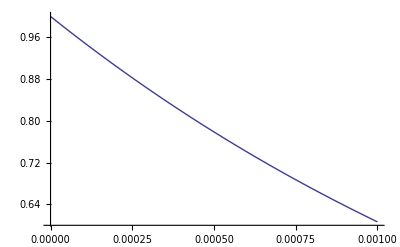

```mathematica
Plot[ⅇ^(-500x),{x,0,.001}]
```

## SVA Model

```mathematica
MassesRobot=Join[ConstantArray[0,nb-1],mm/.constsubs]
```

{0,0,0,0,0,1/10,0,3/2,5,20,5,3/2,0,1/10}

```mathematica
Offsets=Join[ConstantArray[0,{nb-1,3}],JointOffsetsSTT]
Coms=Join[ConstantArray[0,{nb-1,3}],ComOffsetsSTT]
```

(0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
-1/4 | 0 | 1/10
0 | 0 | 0
0 | 0 | 1/2
0 | 0 | 1/2
0 | (p(1))/4 | 0
0 | 0 | -1/2
0 | 0 | -1/2
0 | 0 | 0
1/4 | 0 | -1/10)

(0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
-1/9 | 0 | 1/27
0 | 0 | 0
0 | 0 | 3/8
0 | 0 | 7/40
0 | (p(1))/8 | 3/40
0 | 0 | -13/40
0 | 0 | -1/8
0 | 0 | 0
5/36 | 0 | -17/270)

```mathematica
MakeEffMap[name_?StringQ,linkNumber_?IntegerQ/;0<linkNumber≤nl,linkName_?StringQ,offset_?VectorQ]:=
{
"name"->name,
"dof"->linkNumber-1,
"link"->linkName,
"offset"->offset
}
```

```mathematica
effYAML={
{"stt","SFoot",1},
{"sth","SFoot",1},
{"nst","NSFoot",nl},
{"nsh","NSFoot",nl}
}
```

(stt | SFoot | 1
sth | SFoot | 1
nst | NSFoot | 9
nsh | NSFoot | 9)

```mathematica
ParentOriginsSTT=Join[{{0,0,0}},JointOriginsSTT,1];
```

```mathematica
effMap=(MakeEffMap[#1⟦1⟧,#1⟦3⟧,#1⟦2⟧,EffOriginsFoot⟦EffLabelMap[#1⟦1⟧]⟧-ParentOriginsSTT⟦#1⟦3⟧⟧//N]&)/@effYAML
```

{{name→stt,dof→0,link→SFoot,offset→{0.,0.,0.}},{name→sth,dof→0,link→SFoot,offset→{-0.3125,0.,0.}},{name→nst,dof→8,link→NSFoot,offset→{0.25,0.,-0.1}},{name→nsh,dof→8,link→NSFoot,offset→{-0.0625,0.,-0.1}}}

```mathematica
left={
"coms"->Coms,
"offsets"->ConstantArray[0,{ne,3}],
"preOffsets"->Offsets,
"inertias"->ConstantArray[0,{ne,3,3}],
"extras"->effMap
}/.p[1]->-1//N;
```

```mathematica
right={
"coms"->Coms,
"offsets"->ConstantArray[0,{ne,3}],
"preOffsets"->Offsets,
"inertias"->ConstantArray[0,{ne,3,3}],
"extras"->effMap
}/.p[1]->+1//N;
```

```mathematica
svaModel={
"name"->"3dFoot-amberx",
"nBaseDof"->nb,
"extDof"->TwistAxesExt,
"aniplotNames"->{},
"closedFormJacobianNames"->{},
"sva"->{
"parentDofs"->Range[ne]-1,
"masses"->MassesRobot//N,
"left"->left,
"right"->right
}
}
```

{name→3dFoot-amberx,nBaseDof→6,extDof→{Px,Py,Pz,Rz,Rx,Ry,-Rx,-Ry,-Ry,-Ry,Ry,Ry,Ry,Rx},aniplotNames→{},closedFormJacobianNames→{},sva→{parentDofs→{0,1,2,3,4,5,6,7,8,9,10,11,12,13},masses→{0.,0.,0.,0.,0.,0.1,0.,1.5,5.,20.,5.,1.5,0.,0.1},left→{coms→(0. | 0. | 0.
0. | 0. | 0.
0. | 0. | 0.
0. | 0. | 0.
0. | 0. | 0.
-0.111111 | 0. | 0.037037
0. | 0. | 0.
0. | 0. | 0.375
0. | 0. | 0.175
0. | -0.125 | 0.075
0. | 0. | -0.325
0. | 0. | -0.125
0. | 0. | 0.
0.138889 | 0. | -0.062963),offsets→(0. | 0. | 0.
0. | 0. | 0.
0. | 0. | 0.
0. | 0. | 0.
0. | 0. | 0.
0. | 0. | 0.
0. | 0. | 0.
0. | 0. | 0.
0. | 0. | 0.
0. | 0. | 0.
0. | 0. | 0.
0. | 0. | 0.
0. | 0. | 0.
0. | 0. | 0.),preOffsets→(0. | 0. | 0.
0. | 0. | 0.
0. | 0. | 0.
0. | 0. | 0.
0. | 0. | 0.
-0.25 | 0. | 0.1
0. | 0. | 0.
0. | 0. | 0.5
0. | 0. | 0.5
0. | -0.25 | 0.
0. | 0. | -0.5
0. | 0. | -0.5
0. | 0. | 0.
0.25 | 0. | -0.1),inertias→({0.,0.,0.} | {0.,0.,0.} | {0.,0.,0.}
{0.,0.,0.} | {0.,0.,0.} | {0.,0.,0.}
{0.,0.,0.} | {0.,0.,0.} | {0.,0.,0.}
{0.,0.,0.} | {0.,0.,0.} | {0.,0.,0.}
{0.,0.,0.} | {0.,0.,0.} | {0.,0.,0.}
{0.,0.,0.} | {0.,0.,0.} | {0.,0.,0.}
{0.,0.,0.} | {0.,0.,0.} | {0.,0.,0.}
{0.,0.,0.} | {0.,0.,0.} | {0.,0.,0.}
{0.,0.,0.} | {0.,0.,0.} | {0.,0.,0.}
{0.,0.,0.} | {0.,0.,0.} | {0.,0.,0.}
{0.,0.,0.} | {0.,0.,0.} | {0.,0.,0.}
{0.,0.,0.} | {0.,0.,0.} | {0.,0.,0.}
{0.,0.,0.} | {0.,0.,0.} | {0.,0.,0.}
{0.,0.,0.} | {0.,0.,0.} | {0.,0.,0.}),extras→{{name→stt,dof→0.,link→SFoot,offset→{0.,0.,0.}},{name→sth,dof→0.,link→SFoot,offset→{-0.3125,0.,0.}},{name→nst,dof→8.,link→NSFoot,offset→{0.25,0.,-0.1}},{name→nsh,dof→8.,link→NSFoot,offset→{-0.0625,0.,-0.1}}}},right→{coms→(0. | 0. | 0.
0. | 0. | 0.
0. | 0. | 0.
0. | 0. | 0.
0. | 0. | 0.
-0.111111 | 0. | 0.037037
0. | 0. | 0.
0. | 0. | 0.375
0. | 0. | 0.175
0. | 0.125 | 0.075
0. | 0. | -0.325
0. | 0. | -0.125
0. | 0. | 0.
0.138889 | 0. | -0.062963),offsets→(0. | 0. | 0.
0. | 0. | 0.
0. | 0. | 0.
0. | 0. | 0.
0. | 0. | 0.
0. | 0. | 0.
0. | 0. | 0.
0. | 0. | 0.
0. | 0. | 0.
0. | 0. | 0.
0. | 0. | 0.
0. | 0. | 0.
0. | 0. | 0.
0. | 0. | 0.),preOffsets→(0. | 0. | 0.
0. | 0. | 0.
0. | 0. | 0.
0. | 0. | 0.
0. | 0. | 0.
-0.25 | 0. | 0.1
0. | 0. | 0.
0. | 0. | 0.5
0. | 0. | 0.5
0. | 0.25 | 0.
0. | 0. | -0.5
0. | 0. | -0.5
0. | 0. | 0.
0.25 | 0. | -0.1),inertias→({0.,0.,0.} | {0.,0.,0.} | {0.,0.,0.}
{0.,0.,0.} | {0.,0.,0.} | {0.,0.,0.}
{0.,0.,0.} | {0.,0.,0.} | {0.,0.,0.}
{0.,0.,0.} | {0.,0.,0.} | {0.,0.,0.}
{0.,0.,0.} | {0.,0.,0.} | {0.,0.,0.}
{0.,0.,0.} | {0.,0.,0.} | {0.,0.,0.}
{0.,0.,0.} | {0.,0.,0.} | {0.,0.,0.}
{0.,0.,0.} | {0.,0.,0.} | {0.,0.,0.}
{0.,0.,0.} | {0.,0.,0.} | {0.,0.,0.}
{0.,0.,0.} | {0.,0.,0.} | {0.,0.,0.}
{0.,0.,0.} | {0.,0.,0.} | {0.,0.,0.}
{0.,0.,0.} | {0.,0.,0.} | {0.,0.,0.}
{0.,0.,0.} | {0.,0.,0.} | {0.,0.,0.}
{0.,0.,0.} | {0.,0.,0.} | {0.,0.,0.}),extras→{{name→stt,dof→0.,link→SFoot,offset→{0.,0.,0.}},{name→sth,dof→0.,link→SFoot,offset→{-0.3125,0.,0.}},{name→nst,dof→8.,link→NSFoot,offset→{0.25,0.,-0.1}},{name→nsh,dof→8.,link→NSFoot,offset→{-0.0625,0.,-0.1}}}}}}

```mathematica
YamlWriteFile[svaModel,FileNameJoin[{builddir,"sva-ambersuite.yaml"}]]
```

/home/rsinnet/Documents/MATLAB/kneefoot3d-sva-v30/build_old-model-3d-feet-amber-suite/sva-ambersuite.yaml

### COMPAT: Old form of SVA

```mathematica
leftx={"offsets"->Offsets,"comOffsets"->Coms}/.p[1]->-1//N;
rightx={"offsets"->Offsets,"comOffsets"->Coms}/.p[1]->+1//N;
```

```mathematica
svaModelx={
"nBaseDof"->nb,
"extDof"->TwistAxesExt,
"masses"->MassesRobot//N,
"parentDofs"->Range[ne]-1,
"left"->leftx,
"right"->rightx
}
```

{nBaseDof→6,extDof→{Px,Py,Pz,Rz,Rx,Ry,-Rx,-Ry,-Ry,-Ry,Ry,Ry,Ry,Rx},masses→{0.,0.,0.,0.,0.,0.1,0.,1.5,5.,20.,5.,1.5,0.,0.1},parentDofs→{0,1,2,3,4,5,6,7,8,9,10,11,12,13},left→{offsets→(0. | 0. | 0.
0. | 0. | 0.
0. | 0. | 0.
0. | 0. | 0.
0. | 0. | 0.
-0.25 | 0. | 0.1
0. | 0. | 0.
0. | 0. | 0.5
0. | 0. | 0.5
0. | -0.25 | 0.
0. | 0. | -0.5
0. | 0. | -0.5
0. | 0. | 0.
0.25 | 0. | -0.1),comOffsets→(0. | 0. | 0.
0. | 0. | 0.
0. | 0. | 0.
0. | 0. | 0.
0. | 0. | 0.
-0.111111 | 0. | 0.037037
0. | 0. | 0.
0. | 0. | 0.375
0. | 0. | 0.175
0. | -0.125 | 0.075
0. | 0. | -0.325
0. | 0. | -0.125
0. | 0. | 0.
0.138889 | 0. | -0.062963)},right→{offsets→(0. | 0. | 0.
0. | 0. | 0.
0. | 0. | 0.
0. | 0. | 0.
0. | 0. | 0.
-0.25 | 0. | 0.1
0. | 0. | 0.
0. | 0. | 0.5
0. | 0. | 0.5
0. | 0.25 | 0.
0. | 0. | -0.5
0. | 0. | -0.5
0. | 0. | 0.
0.25 | 0. | -0.1),comOffsets→(0. | 0. | 0.
0. | 0. | 0.
0. | 0. | 0.
0. | 0. | 0.
0. | 0. | 0.
-0.111111 | 0. | 0.037037
0. | 0. | 0.
0. | 0. | 0.375
0. | 0. | 0.175
0. | 0.125 | 0.075
0. | 0. | -0.325
0. | 0. | -0.125
0. | 0. | 0.
0.138889 | 0. | -0.062963)}}

```mathematica
YamlWriteFile[svaModelx,FileNameJoin[{builddir,"sva.yaml"}]]
```

/home/rsinnet/Documents/MATLAB/kneefoot3d-sva-v30/build_old-model-3d-feet-amber-suite/sva.yaml

## Conversion to MATLAB

```mathematica
Run["perl "<>FileNameJoin[{utildir,"math2mat.pl"}]<>" "<>builddir<>" "<>builddir]
```

0

```mathematica
dl2=DateString[]
```

Tue 23 Jul 2013 15:55:46

```mathematica
Print["Computation time:      "<>ToString[DateDifference[dl1,dl2,"Second"]//First]<>" seconds"];
```

Computation time:      324. seconds

## Conversion to CPP

```mathematica
Clear[getCFormNoPowers];
getCFormNoPowers[expr_]:=Module[{times},Apply[Function[code,Hold[CForm[code]],HoldAll],Hold[#]&[expr/.x_Symbol^y_Integer/;3>y>1:>times@@Table[x,{y}]]/.times->Times]];
```

```mathematica
(*Ccform=String[HoldForm@@getCFormNoPowers[Flatten[Cαζ]/.Ζxsubs/.Cstatesubs]];*)
```

```mathematica
Cstatesubs=Join[
(Q⟦#+1⟧->HoldForm@q⟦#⟧&/@(Range[ne]-1)),
(dQ⟦#+1⟧->HoldForm@dq⟦#⟧&/@(Range[ne]-1)),
(p[#+1]->HoldForm@p⟦#⟧&/@(Range[np]-1))
]
```

{p_x(t)→q⟦0⟧,p_y(t)→q⟦1⟧,p_z(t)→q⟦2⟧,q_z(t)→q⟦3⟧,q_x(t)→q⟦4⟧,q_y(t)→q⟦5⟧,q_1(t)→q⟦6⟧,q_2(t)→q⟦7⟧,q_3(t)→q⟦8⟧,q_4(t)→q⟦9⟧,q_5(t)→q⟦10⟧,q_6(t)→q⟦11⟧,q_7(t)→q⟦12⟧,q_8(t)→q⟦13⟧,p_x'(t)→dq⟦0⟧,p_y'(t)→dq⟦1⟧,p_z'(t)→dq⟦2⟧,q_z'(t)→dq⟦3⟧,q_x'(t)→dq⟦4⟧,q_y'(t)→dq⟦5⟧,q_1'(t)→dq⟦6⟧,q_2'(t)→dq⟦7⟧,q_3'(t)→dq⟦8⟧,q_4'(t)→dq⟦9⟧,q_5'(t)→dq⟦10⟧,q_6'(t)→dq⟦11⟧,q_7'(t)→dq⟦12⟧,q_8'(t)→dq⟦13⟧,p(1)→p⟦0⟧,p(2)→p⟦1⟧,p(3)→p⟦2⟧}

```mathematica
ToCForm[expr_?MatrixQ]:=Flatten@(exprᵀ)/.Ζxsubs/.Cstatesubs;
ToCForm[expr_?VectorQ[expr]]:=expr/.Ζxsubs/.Cstatesubs;
ToCForm[expr_/;!ListQ[expr]]:=Flatten@expr/.Ζxsubs/.Cstatesubs;
```

```mathematica
DDfχz=ParallelSimplify[DDfχ/.Ζsubs];
(*WriteExprζ[DDfχz,"DM1Dqzmat"];*)
```

```mathematica
Mcform=ToCForm@Dαζ;
Ccform=ToCForm@Cαζ;
Gcform=ToCForm@Gαζ;
ELWcform=ToCForm@ELWαζ;
DM1Dqcform=ToCForm@DDfχz;
plotposcform=ToCForm@ppζ;
hnshcform=ToCForm@pnsh⟦3⟧;
hnstcform=ToCForm@pnst⟦3⟧;
```

#### Splice code into templates

```mathematica
MakeCpp[file_?StringQ]:=
Splice[FileNameJoin[{nbdir,"templates",file<>".mcc"}],FileNameJoin[{builddir,file<>".cc"}]]
```

```mathematica
MakeCpp["CShaped"];
MakeCpp["MShaped"];
MakeCpp["GShaped"];
MakeCpp["ELWShaped"];
MakeCpp["DM1DqShaped"];
MakeCpp["PlotPositions"];
MakeCpp["HeightNSH"];
MakeCpp["HeightNST"];
```